# Cálculo Numérico (MAT012) Atividade 01

## Universidade Federal de Itajubá UNIFEI

Luis Roberto Costa Dias - 21783
Fernando Belo Anacleto Granco - 22007

Letra A)

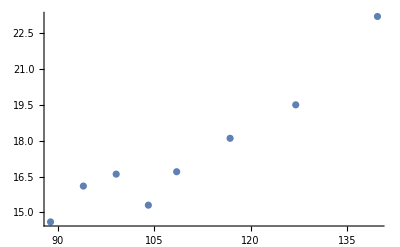

```mathematica
pontos={{88.9,14.6},{108.5,16.7},{104.1,15.3},{139.7,23.2},{127,19.5},{94,16.1},{116.8,18.1},{99.1,16.6}};
x1=ListPlot[pontos]
Clear[x]
```

Letra B Item 1)

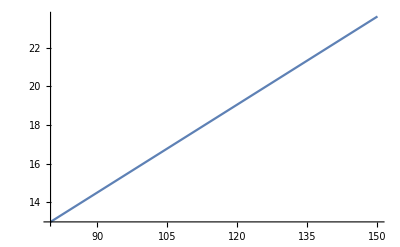

```mathematica
a=0.151871;
b=0.842783;
Fp=a*xfp+b;
Plot[Fp,{xfp,80,150}]
```

Letra B Item 2)

```mathematica
Y=Fit[pontos,{1,x},x]
```

0.842783+0.151871 x

Letra B Item 3)

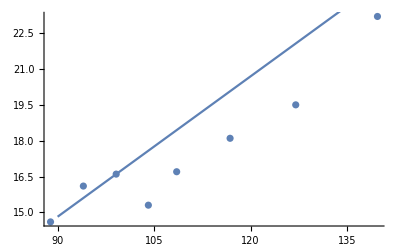

```mathematica
Show[x1,Plot[Fp,{x,90,145}]]
```

Letra C)

```mathematica
xc=120;
Print["Valor de F(120) = ",0.8427826132028933+0.15187078817261906* xc]
```

Valor de F(120) = 19.0673

Letra D)

```mathematica
Print["O valor pela função InterpolatingPolynomial para F(x) = ",InterpolatingPolynomial[pontos,x]]
Print["O valor pela função InterpolatingPolynomial para F(120) = ",InterpolatingPolynomial[pontos,xc]]
```

O valor pela função InterpolatingPolynomial para F(x) = 23.2+(0.169291+(0.00191456+(0.000145443+(-6.84274×10^-7+(3.25839×10^-7+(3.63548×10^-8-3.62586×10^-8 (-108.5+x)) (-94+x)) (-127+x)) (-99.1+x)) (-116.8+x)) (-88.9+x)) (-139.7+x)

O valor pela função InterpolatingPolynomial para F(120) = 15.6898

#### Conclusão

Foi possível observar a diferença entre os valores obtidos utilizando os diferentes métodos disponíveis, bem como observar a precisão de cada método, variando conforme o grau da equação, sendo a interpolação polinomial a mais precisa. Além disso, foi possível constatar que a função Fit[] utilizasse do método de Quadrados Mínimos Lineares.